```mathematica
ZrC density of states and Einstein thermodynamic analysis;
```

Test the variational Gauss-broadened Einstein model

```mathematica
Some basic information;
aLabel={"4.575","4.600","4.625","4.6583","4.685","4.730","4.759","4.801","4.850"};
ePeRF={-673.82051,-674.79111,-675.40188,-675.68572,-675.50095,-674.41442,-673.23280,-670.90290,-667.33277};
eFren={-669.60769,-670.75114,-671.53884,-672.06424,-672.07754,-671.33314,-670.37803,-668.38638,-665.23097};
eCvac={-662.57856,-663.53617,-664.14458,-664.44074,-664.27725,-663.24766,-662.11597,-659.87660,-656.43966};
eZvac={-655.35351,-656.24549,-656.79543,-657.02389,-656.81424,-655.72117,-654.55722,-652.28142,-648.81500};
ePerfat=1000*ePeRF/64;eFrenat=1000*eFren/64;eCvacat=1000*eCvac/63;eZvacat=1000*eZvac/63;
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
Nqha=9;
```

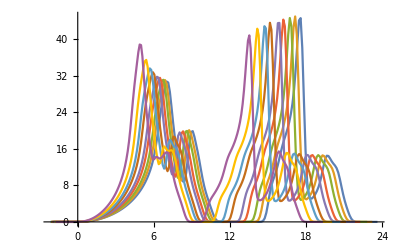

```mathematica
Import data;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/PERF_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllPERF=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllPERF
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/FREN_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllFREN=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllFREN;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/CVAC_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllCVAC=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllCVAC;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/ZVAC_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllZVAC=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllZVAC;
```

```mathematica
Fit DOS using Mathematica interpolation routines;
PERFdosFITs=Table[Interpolation[dosAllPERF[[i]]],{i,1,9}];
FRENdosFITs=Table[Interpolation[dosAllFREN[[i]]],{i,1,9}];
CVACdosFITs=Table[Interpolation[dosAllCVAC[[i]]],{i,1,9}];
ZVACdosFITs=Table[Interpolation[dosAllZVAC[[i]]],{i,1,9}];
```

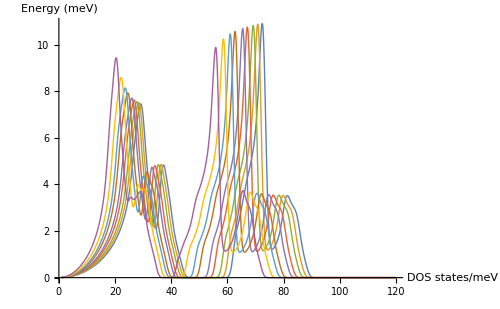

```mathematica
Plot interpolated DOS in meV ;
Plot[Evaluate@Table[THz2meV*PERFdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
Plot[Evaluate@Table[THz2meV*FRENdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}];
Plot[Evaluate@Table[THz2meV*CVACdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}];
Plot[Evaluate@Table[THz2meV*ZVACdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}];
```

```mathematica
Check number of modes;
Emin=0;Emax=120;
192 modes;
Table[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
Table[NIntegrate[(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
189 modes;
Table[NIntegrate[(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
Table[NIntegrate[(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
```

{191.999,191.999,191.999,191.999,191.999,191.999,191.999,191.999,191.999}

{191.996,191.998,191.998,191.998,191.998,191.998,191.998,191.997,191.995}

{188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999}

{188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999}

```mathematica
Get lower and upper band centres for PERF;
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
Off[FindMaximum::cvmit]
(*Get the lower band centres - median and mode*)
(*Excuse the hacky way to extract peaks maxima in phonon DOS*)
"Lower PERF mode:"
lowerPERFmode=Table[FindMaximum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],0<energy<31-i},energy][[2]][[1]][[2]],{i,1,9}]
"Lower PERF median:"
lowerPERFmedian=Table[medianLowerBand/.FindRoot[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,0,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,9}]
(*Extract a mid point where the DOS goes to zero*)
"PERF DOS zero midpoints:"
midpointPERF=
Table[FindMinimum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],energy>39.1},energy][[2]][[1]][[2]],{i,1,9}]
(*Get the upper band centres - median and mode*)
Off[InterpolatingFunction::dmval]
Off[General::stop]
"Upper PERF mode:"
upperPERFmode=Table[FindMaximum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],energy>62-2.2*i},energy][[2]][[1]][[2]],{i,1,9}]
"Upper PERF median:"
upperPERFmedian=
Table[medianUpperBand/.FindRoot[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,midpointPERF[[i]],medianUpperBand}]-48==0,{medianUpperBand,60}],{i,1,9}]
```

Lower PERF mode:

{29.1337,28.43,27.7414,26.7766,25.963,24.5468,23.6067,22.1858,20.3726}

Lower PERF median:

{29.5568,28.8407,28.1188,27.1387,26.3401,24.9507,24.026,22.6324,20.9013}

PERF DOS zero midpoints:

{47.4985,56.8159,54.3598,44.2896,43.4227,41.6063,40.6833,40.1926,39.1005}

Upper PERF mode:

{72.3864,70.7944,69.1689,67.0743,65.4438,62.7025,60.9981,58.563,55.8259}

Upper PERF median:

{72.1926,70.5744,68.9623,66.8316,65.1587,62.3896,60.6454,58.179,55.3849}

```mathematica
Hessian diagonal elements 1 and 192;
lowerPERFhess={0.227134990752235782,0.215629510044018896,0.204482192291760928,0.190171820406654507,0.179255218502894081,0.161823568215306995,0.151273943385760723,0.136865113734847693,0.121304891648369606};
upperPERFhess={0.158410899076719930,0.151742568391175114,0.145176379597923289,0.136639707968101709,0.130071877783300593,0.119478182362475024,0.112988572974945550,0.104053449687505489,0.0942772701666999002};
(*Note the Frenkel Hessian has to be resubmitted as rearranged!, and the Hessian Einstein constants extracted carefully taking into accuont defect position*)
lowerFRENhess={0.217730563262878152,0.206174806577149372,0.195055773242902186,0.180906947216968150,0.170066456484977313,0.152784347772913387,0.142247699712918563,0.127777716649587952E,0.111956137690552585};
upperFRENhess={0.159420416624561911,0.153008446600934017,0.146795537752417687,0.138830137272252602,0.132679318304059657,0.122799798006224523,0.116749314885077782,0.108444341880512066,0.994799102348783298};
(*tamellan@tycpc34:/workspace/tamellan/Tessa_ZrC/700_666/CVAC_REARRANGE/HesseMatrix_rearr*)
(*CVAC has 4 species, with Zr vac NN and C vac NN having two types of force constant with different degeneracies - for the time being only consider the normal sites in the CVAC crystal*)
(*lowerCVAChess={};upperCVAChess={};*)
lowerCVAChess={0.226439282570529726,0.214839223749259012,0.203702927503891823,0.189517249922237591,0.178723716366664315,0.161451898510707709,0.150953424381442936,0.136562397911595523,0.120953922000830133};
upperCVAChess={0.159958639714926965,0.156117018908149746,0.152352691571383175,0.147465455006159207,0.143695990295091086,0.137616067897763844,0.133936791029598351,0.129008164400599423,0.123981360074614633};
```

```mathematica
Convert the Hessian diagonals to Einstein frequencies;
hessToEinZr[arg_]:=2Sqrt[arg/HarBohr/mass[[1]]]
hessToEinC[arg_]:=2Sqrt[arg/HarBohr/mass[[2]]]
lowerPERFhessEin=hessToEinZr[lowerPERFhess]
upperPERFhessEin=hessToEinC[upperPERFhess]
lowerFRENhessEin=hessToEinZr[lowerFRENhess]
upperFRENhessEin=hessToEinC[upperFRENhess]
lowerCVAChessEin=hessToEinZr[lowerCVAChess]
upperCVAChessEin=hessToEinC[upperCVAChess]
```

{31.1094,30.3112,29.5174,28.4658,27.6367,26.2585,25.3882,24.1488,22.7347}

{71.5999,70.0767,68.5438,66.498,64.8801,62.182,60.4696,58.0294,55.2362}

{30.4586,29.6393,28.829,27.7637,26.919,25.5146,24.6191,38.4702,21.8411}

{71.8277,70.3684,68.925,67.0289,65.5272,63.0404,61.4677,59.2412,179.427}

{31.0617,30.2557,29.4611,28.4167,27.5957,26.2284,25.3613,24.1221,22.7018}

{71.9489,71.0796,70.2175,69.0821,68.1934,66.7352,65.837,64.6143,63.343}

```mathematica
Einstein frequencies:
1) EinMedian - Extracted as the energy of the 48th mode  (there are 96 modes per super-cell species)
2) EinMode - The frequency corresponding to the highest peak in each band of the DOS
3) EinHess - The frequency extract from the diagonal elements of the Hessian
```

```mathematica
(*These omega0s can be used to generate the vibrational excitation spectrums ie E=hbar*omega(n+0.5)*)
medianEin={Transpose@{lowerPERFmedian,upperPERFmedian}};
modeEin={Transpose@{lowerPERFmode,upperPERFmode}};
hessEin={Transpose@{lowerPERFhessEin,upperPERFhessEin},Transpose@{lowerFRENhessEin,upperFRENhessEin},Transpose@{lowerCVAChessEin,upperCVAChessEin}};
```

```mathematica
1) Easy method - Harmonic approximation heat capacity expression (phonopy website);
```

```mathematica
Cv[T_,freqs_,dosfactor_,freqfactor_]:=dosfactor*(K2meV*((((freqfactor*freqs))/(K2meV*T))^2)*Exp[((freqfactor*freqs))/(K2meV*T)]/((Exp[((freqfactor*freqs))/(K2meV*T)]-1)^2))
```

29.5568

72.1926

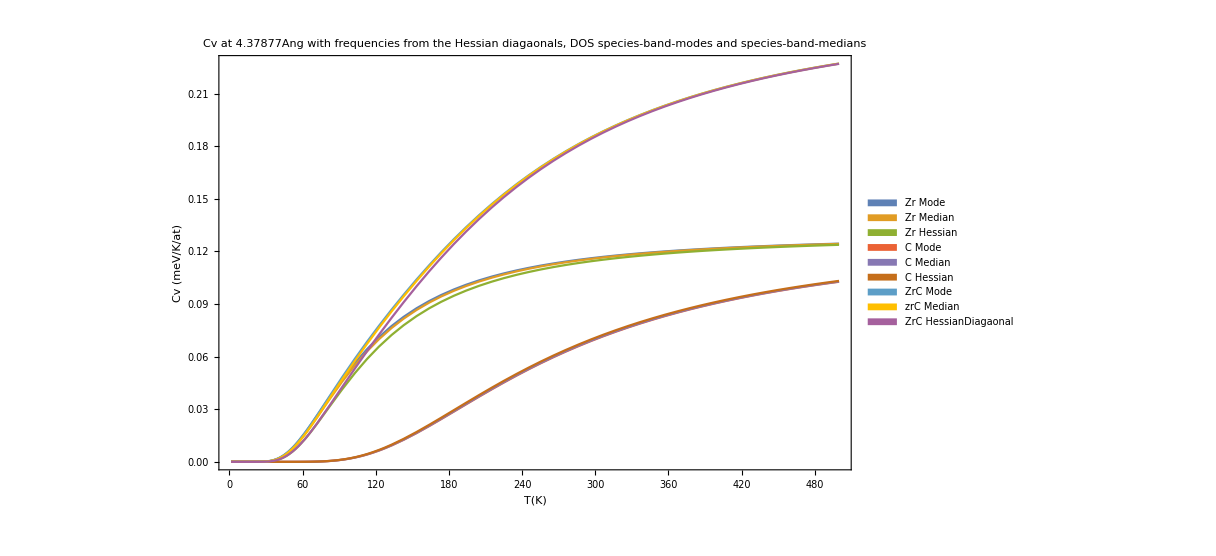

```mathematica
medianEin[[1]][[1]][[1]]
medianEin[[1]][[1]][[2]]

Plot[{{Cv[T,modeEin[[1]][[1]][[1]],3/2,1],Cv[T,medianEin[[1]][[1]][[1]],3/2,1],Cv[T,hessEin[[1]][[1]][[1]],3/2,1]},{Cv[T,modeEin[[1]][[1]][[2]],3/2,1],Cv[T,medianEin[[1]][[1]][[2]],3/2,1],Cv[T,hessEin[[1]][[1]][[2]],3/2,1]},{Cv[T,modeEin[[1]][[1]][[1]],3/2,1]+Cv[T,modeEin[[1]][[1]][[2]],3/2,1],Cv[T,medianEin[[1]][[1]][[1]],3/2,1]+Cv[T,medianEin[[1]][[1]][[2]],3/2,1],Cv[T,hessEin[[1]][[1]][[1]],3/2,1]+Cv[T,hessEin[[1]][[1]][[2]],3/2,1]}},{T,1,500},PlotRange->All,PlotLabel->"Cv at 4.37877Ang with frequencies from the Hessian diagaonals,\n DOS species-band-modes and species-band-medians",PlotLegends->SwatchLegend[{"Zr Mode","Zr Median","Zr Hessian","C Mode","C Median","C Hessian","ZrC Mode","zrC Median","ZrC HessianDiagaonal","Phonopy full phonon Cv"}],FrameLabel->{"T(K)","Cv (meV/K/at)"},Frame->True,ImageSize->900]
```

```mathematica
2) General method  Heat Capacity via Free Energy from partition function;
```

```mathematica
(*Define free energy as log partition function and make excitation spectrum from the omega0 obtained from DOS median, mode, and Hessian*)
(*indicies*)
(*medianEin[[Crystal:PERF|FREN|CVAC]][[Volumes:1||9]][[Element:1|2]]*)

(*Free energy*)
frGauss[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=Integrate[-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}],{energy,0,1000}]

(*Makes list of the excited states of the omega0 Einstein frequency - range 1 to maxval*)
maxval=200;
spectrumCmedian=Table[Table[medianEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
spectrumZmedian=Table[Table[medianEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
spectrumCmode=Table[Table[modeEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
spectrumZmode=Table[Table[modeEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
spectrumChess=Table[Table[hessEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
spectrumZhess=Table[Table[hessEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,Nqha}];
```

```mathematica
E0 Volume dependence at zero temperature excluding ZP effects;
```

```mathematica
(*Perf*)
eafitPerf=Fit[Transpose[{alatts,ePerfat}],{1,x,x*x,x*x*x},x]
eafitMinPerf=FindMinimum[Evaluate@eafitPerf,x][[1]]
e0Perf=ePerfat[[1;;9]]-eafitMinPerf
```

322945.-196102. x+38087.3 x^2-2438.45 x^3

-10557.6

{29.1486,13.983,4.43971,0.00471107,2.89174,19.8688,38.3316,74.7363,130.52}

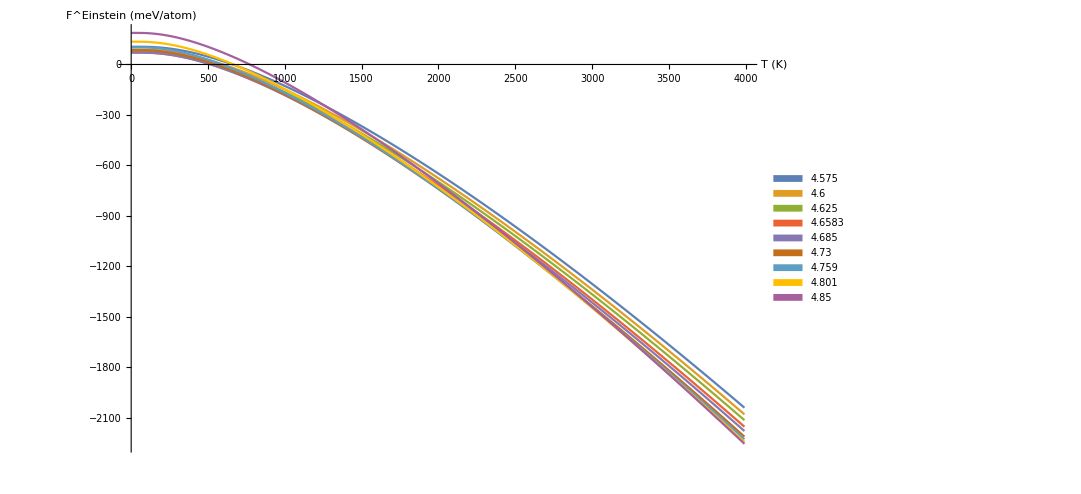

(ⅇ^(-(-36.0963+x)^2/1800))/(30 √(2 π))

```mathematica
(*Plot Helmboltz free energy*)
minT=1;maxT=4000;dT=10;
ListLinePlot[Table[Table[{t,e0Perf[[k]]+Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],maxval,1,1.5]},{t,minT,maxT,dT}],{k,1,Nqha}],PlotLegends->SwatchLegend[alatts],ImageSize->800,AxesLabel->{"T (K)","F^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

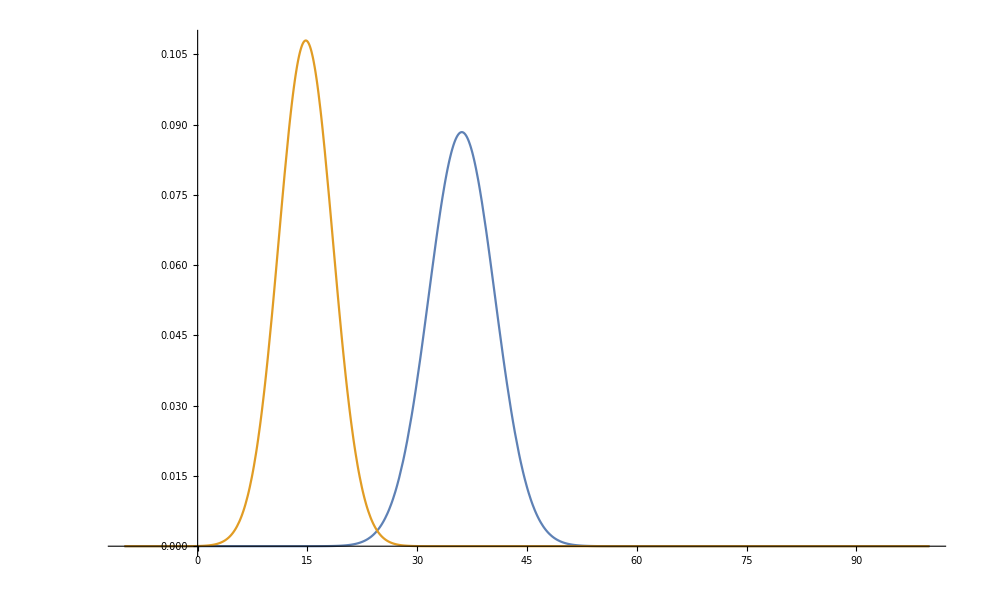

```mathematica
Plot[{PDF[NormalDistribution[spectrumCmedian[[1]][[1]],spectrumCmedian[[1]][[1]]/8],x],PDF[NormalDistribution[spectrumZmedian[[1]][[1]],spectrumZmedian[[1]][[1]]/4],x]},{x,-10,100},PlotRange->All]
```

```mathematica
spectrumCmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[2]]*(j-0.5),medianEin[[1]][[k]][[2]]*(j-0.5)*0.125],x],{j,1,maxval}],{k,1,Nqha}];
spectrumZmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[1]]*(j-0.5),medianEin[[1]][[k]][[1]]*(j-0.5)*0.25],x],{j,1,maxval}],{k,1,Nqha}];
```

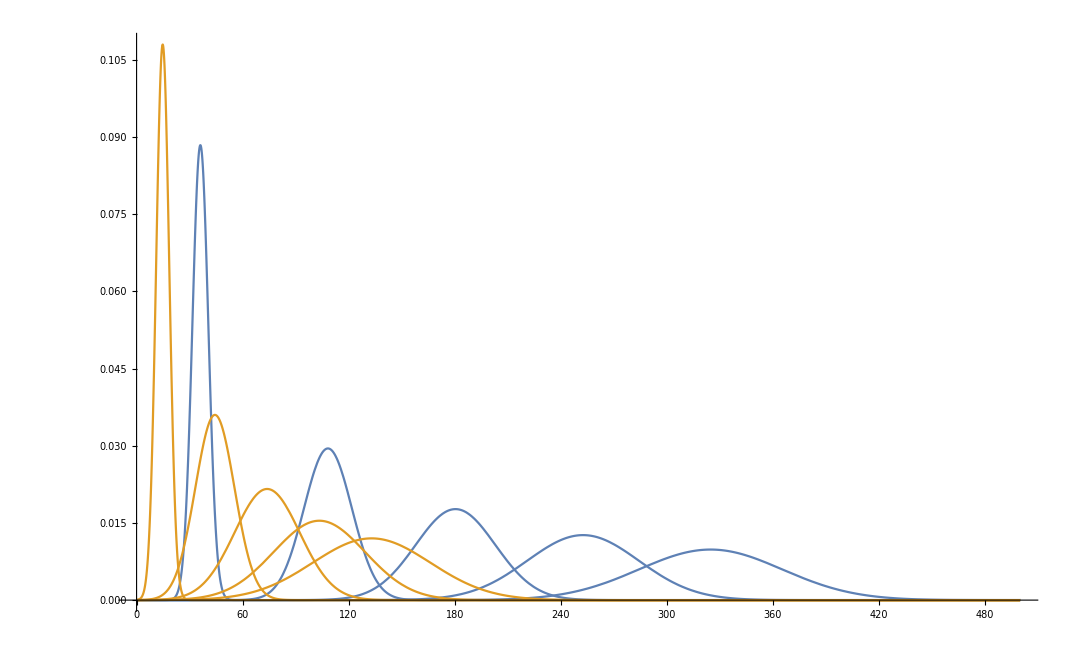

```mathematica
Plot[{spectrumCmedianG[[1]][[1;;5]],spectrumZmedianG[[1]][[1;;5]]},{x,0,500},PlotRange->All]
```

```mathematica
minT=1;maxT=4000;dT=10;
ListLinePlot[Table[Table[{t,e0Perf[[k]]+Total@fr[t,spectrumCmedianG[[k]],spectrumZmedianG[[k]],maxval,1,1.5]},{t,minT,maxT,dT}],{k,1,Nqha}],PlotLegends->SwatchLegend[alatts],ImageSize->800,AxesLabel->{"T (K)","F^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

```mathematica
(*Free energy*)
frGauss[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=Integrate[-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}],{x,0,100000}]
```

```mathematica
minT=1;maxT=40;dT=10;Nqha=1;maxval=5;
spectrumCmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[2]]*(j-0.5),medianEin[[1]][[k]][[2]]*(j-0.5)*0.125],x],{j,1,maxval}],{k,1,Nqha}];
spectrumZmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[1]]*(j-0.5),medianEin[[1]][[k]][[1]]*(j-0.5)*0.25],x],{j,1,maxval}],{k,1,Nqha}];
```

```mathematica
spectrumZmedianG[[1]][[1]]
Integrate[spectrumZmedianG[[1]][[1]],{x,0,100000}]
```

0.10798 ⅇ^(-0.0366299 (-14.7784+x)^2)

0.999968

```mathematica
edos=Table[{dosAllPERF[[1]][[i]][[1]]/THz2meV,dosAllPERF[[1]][[i]][[2]]THz2meV},{i,1,dosAllPERF[[1]]//Length}][[18;;]];
Edos=Table[{dosAllPERF[[1]][[i]][[1]]/THz2meV,dosAllPERF[[1]][[i]][[2]]THz2meV},{i,1,dosAllPERF[[1]]//Length}];
interEdos=Interpolation[Edos];
```

```mathematica
(*http://www.physics.smu.edu/scalise/P5337sp16/albert/chapter5.pdf*)
```

```mathematica
CC[T_,freqs_,dosfactor_,freqfactor_]:=dosfactor*(K2meV*((((freqfactor*freqs))/(K2meV*T))^2)*Exp[((freqfactor*freqs))/(K2meV*T)]/((Exp[((freqfactor*freqs))/(K2meV*T)]-1)^2))
```

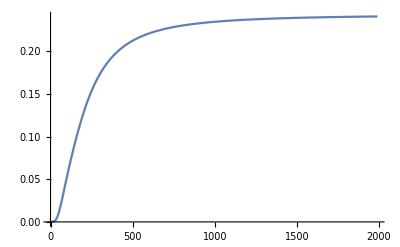

```mathematica
a=ListLinePlot[Table[{t,Total@Table[CC[t,edos[[i]][[1]]+0.000000001,edos[[i]][[2]]/128,1],{i,1,Length[edos]}]},{t,1,2000,10}],PlotRange->All]
```

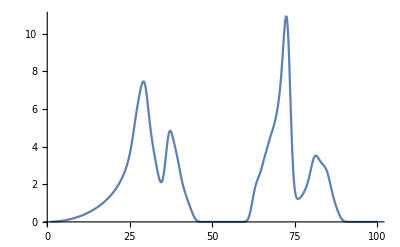

```mathematica
Plot[interEdos[e],{e,1,100}]
```

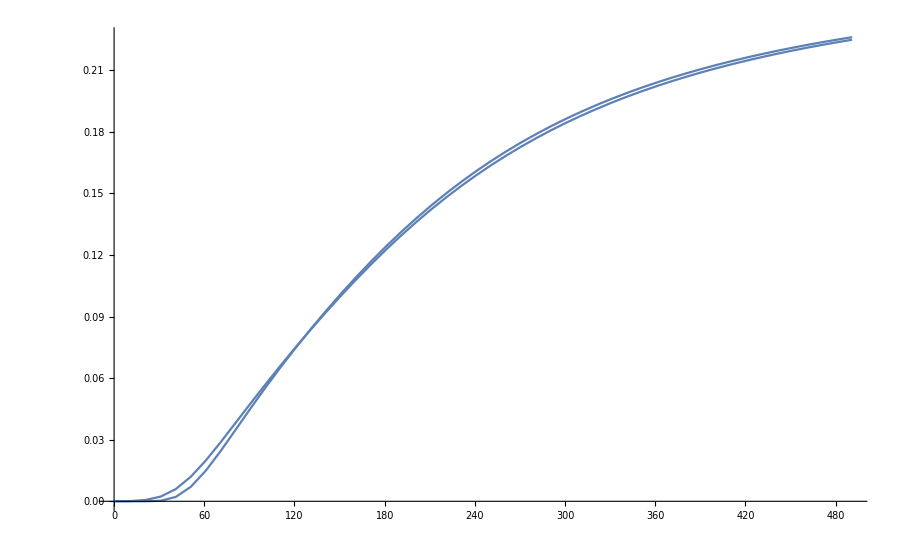

```mathematica
Show[{ListLinePlot@Table[{t,Total@{CC[t,medianEin[[1]][[1]][[2]],1.5,1],CC[t,medianEin[[1]][[1]][[1]],1.5,1]}},{t,1,500,10}],
ListLinePlot@Table[{t,Total@Table[CC[t,e,0.125*interEdos[e]/Nat,1],{e,1,90,0.125}]},{t,1,500,10}]}]
```

29.5568

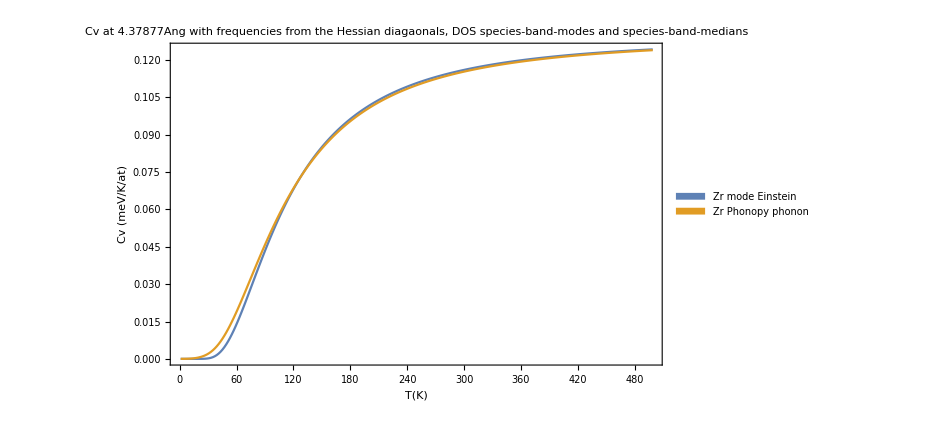

```mathematica
medianEin[[1]][[1]][[1]]
ListLinePlot[{Table[{t,CC[t,medianEin[[1]][[1]][[1]],1.5,1]},{t,1,500,2}],
Table[{t,Total@Table[CC[t,e,0.125*interEdos[e]/Nat,1],{e,1,50,0.125}]},{t,1,500,2}]},PlotLabel->"Cv at 4.37877Ang with frequencies from the Hessian diagaonals,\n DOS species-band-modes and species-band-medians",PlotLegends->SwatchLegend[{"Zr mode Einstein","Zr Phonopy phonon"}],FrameLabel->{"T(K)","Cv (meV/K/at)"},Frame->True,ImageSize->700]
```

```mathematica
PDF[NormalDistribution[medianEin[[1]][[k]][[2]]*(j-0.5),medianEin[[1]][[k]][[2]]*(j-0.5)*0.125],x],{j,1,maxval}],{k,1,Nqha}];
```

```mathematica
(*medianEin[[1]][[vol]][[element]]*)
```

{6.29643 ⅇ^(-0.0135144 (-24.3303+e)^2),6.92734 ⅇ^(-0.0163584 (-22.1144+e)^2),7.29368 ⅇ^(-0.0181343 (-21.0036+e)^2),7.70328 ⅇ^(-0.0202283 (-19.8868+e)^2),8.16815 ⅇ^(-0.0227434 (-18.755+e)^2),8.70563 ⅇ^(-0.0258349 (-17.5971+e)^2),9.34417 ⅇ^(-0.0297638 (-16.3946+e)^2),10.1309 ⅇ^(-0.0349868 (-15.1214+e)^2),11.1419 ⅇ^(-0.0423182 (-13.7493+e)^2)}

{8.99865 ⅇ^(-0.0276034 (-85.1204+e)^2),9.8274 ⅇ^(-0.0329219 (-77.9422+e)^2),10.2805 ⅇ^(-0.0360279 (-74.5067+e)^2),10.763 ⅇ^(-0.0394888 (-71.1669+e)^2),11.2816 ⅇ^(-0.0433861 (-67.8953+e)^2),11.8436 ⅇ^(-0.0478163 (-64.6736+e)^2),12.4544 ⅇ^(-0.0528752 (-61.502+e)^2),13.1189 ⅇ^(-0.0586683 (-58.3866+e)^2),13.8437 ⅇ^(-0.0653301 (-55.3297+e)^2)}

{8.99865 ⅇ^(-0.0276034 (-85.1204+e)^2)+6.29643 ⅇ^(-0.0135144 (-24.3303+e)^2),9.8274 ⅇ^(-0.0329219 (-77.9422+e)^2)+6.92734 ⅇ^(-0.0163584 (-22.1144+e)^2),10.2805 ⅇ^(-0.0360279 (-74.5067+e)^2)+7.29368 ⅇ^(-0.0181343 (-21.0036+e)^2),10.763 ⅇ^(-0.0394888 (-71.1669+e)^2)+7.70328 ⅇ^(-0.0202283 (-19.8868+e)^2),11.2816 ⅇ^(-0.0433861 (-67.8953+e)^2)+8.16815 ⅇ^(-0.0227434 (-18.755+e)^2),11.8436 ⅇ^(-0.0478163 (-64.6736+e)^2)+8.70563 ⅇ^(-0.0258349 (-17.5971+e)^2),12.4544 ⅇ^(-0.0528752 (-61.502+e)^2)+9.34417 ⅇ^(-0.0297638 (-16.3946+e)^2),13.1189 ⅇ^(-0.0586683 (-58.3866+e)^2)+10.1309 ⅇ^(-0.0349868 (-15.1214+e)^2),13.8437 ⅇ^(-0.0653301 (-55.3297+e)^2)+11.1419 ⅇ^(-0.0423182 (-13.7493+e)^2)}

96 (Piecewise[{{0.104808 ⅇ^(-0.209615 (-24.3303+e)), e≥24.3303}, {0.104808 ⅇ^(-0.209615 (24.3303-e)), True}}])

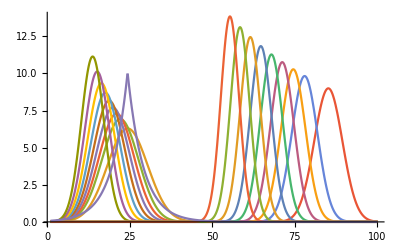

```mathematica
gaussZr=Table[(3Nat/2)PDF[NormalDistribution[medianEin[[1]][[vol]][[1]],medianEin[[1]][[vol]][[1]]/4],e],{vol,1,9}]
gaussC=Table[(3Nat/2)PDF[NormalDistribution[medianEin[[1]][[vol]][[2]],medianEin[[1]][[vol]][[2]]/20],e],{vol,1,9}]
gauss=gaussZr+gaussC
laplaceZr=(3Nat/2)PDF[LaplaceDistribution[medianEin[[1]][[1]][[1]],medianEin[[1]][[1]][[1]]/5.1],e]
Plot[{interEdos[e],gaussZr,gaussC,laplaceZr},{e,1,100},PlotRange->All]
(*Debye - http://dao.mit.edu/8.231/Thermal.pdf*)
```

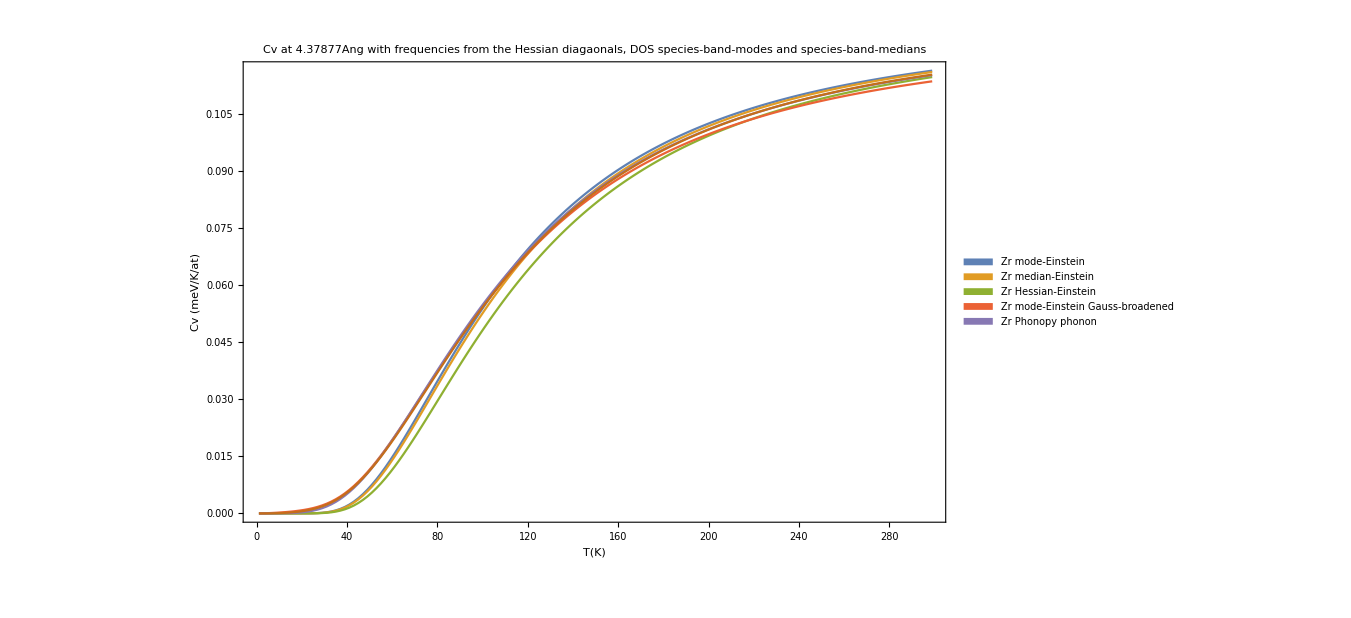

```mathematica
ListLinePlot[{Table[{t,CC[t,modeEin[[1]][[1]][[1]],1.5,1]},{t,1,300,2}],Table[{t,CC[t,medianEin[[1]][[1]][[1]],1.5,1]},{t,1,300,2}],Table[{t,CC[t,hessEin[[1]][[1]][[1]],1.5,1]},{t,1,300,2}],Table[{t,Total@Table[CC[t,e,0.125*laplaceZr/Nat,1],{e,1,50,0.125}]},{t,1,300,2}],
Table[{t,Total@Table[CC[t,e,0.125*gaussZr/Nat,1],{e,1,50,0.125}]},{t,1,300,2}],Table[{t,Total@Table[CC[t,e,0.125*interEdos[e]/Nat,1],{e,1,50,0.125}]},{t,1,300,2}]},PlotLabel->"Cv at 4.37877Ang with frequencies from the Hessian diagaonals,\n DOS species-band-modes and species-band-medians",PlotLegends->SwatchLegend[{"Zr mode-Einstein","Zr median-Einstein","Zr Hessian-Einstein","Zr mode-Einstein Gauss-broadened","Zr Phonopy phonon"}],FrameLabel->{"T(K)","Cv (meV/K/at)"},Frame->True,ImageSize->1000]
```

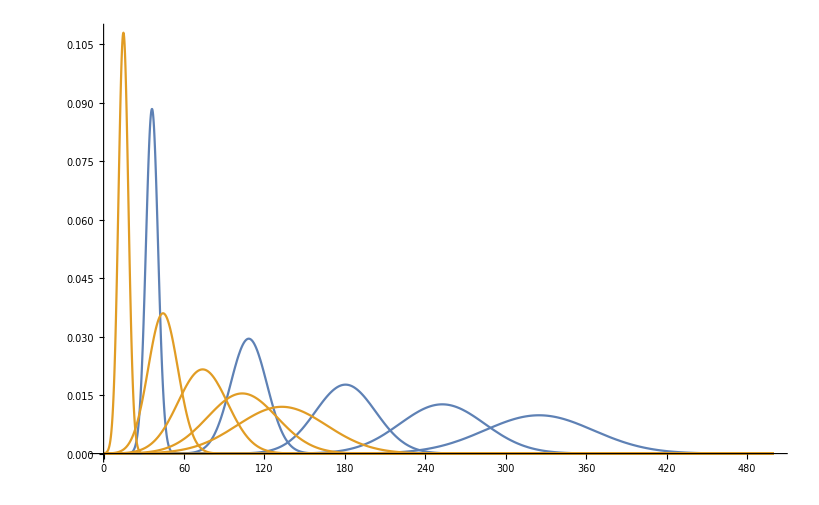

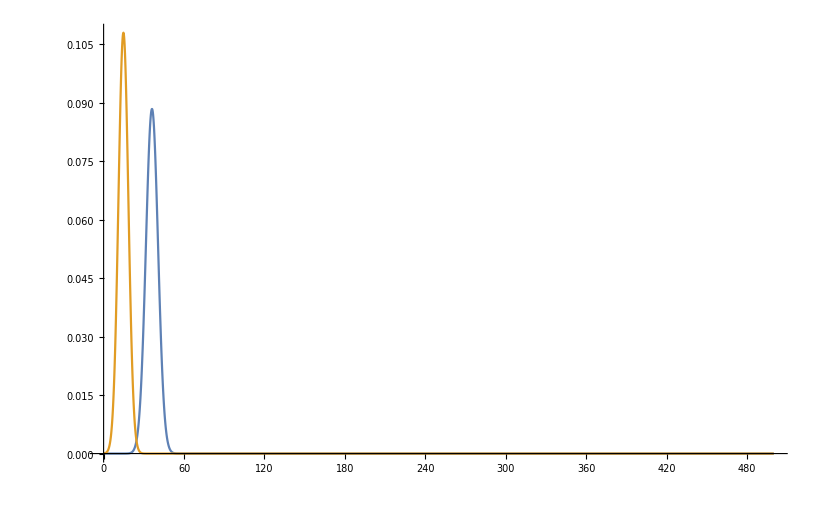

```mathematica
maxval=10;
spectrumCmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[2]]*(j-0.5),medianEin[[1]][[k]][[2]]*(j-0.5)*0.125],x],{j,1,maxval}],{k,1,Nqha}];
spectrumZmedianG=Table[Table[PDF[NormalDistribution[medianEin[[1]][[k]][[1]]*(j-0.5),medianEin[[1]][[k]][[1]]*(j-0.5)*0.25],x],{j,1,maxval}],{k,1,Nqha}];
Plot[{spectrumCmedianG[[1]][[1;;5]],spectrumZmedianG[[1]][[1;;5]]},{x,0,500},PlotRange->All]
Plot[{spectrumCmedianG[[1]][[1]],spectrumZmedianG[[1]][[1]]},{x,0,500},PlotRange->All]
```

```mathematica
Plot[{Exp[-Abs[x-5]],-Abs[x^2-5^2]+25},{x,-1,10}]
```

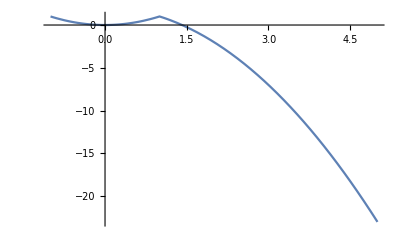

```mathematica
Plot[{-Abs[x^2-1]+1},{x,-1,5}]
```

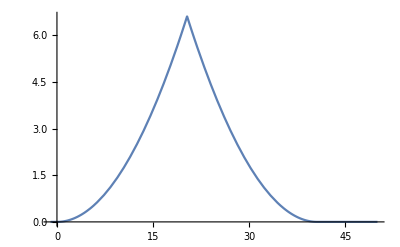

```mathematica
f[x_,m_]:=If[-m<x<0,(x+m)^2,If[ 0<x<m,(x-m)^2,0],0]
g[x_,m_]:=f[x-m,m]/m^2*((3*96)^(1/3)//N)
Plot[g[x,20.3],{x,-1,50},PlotRange->All]
```

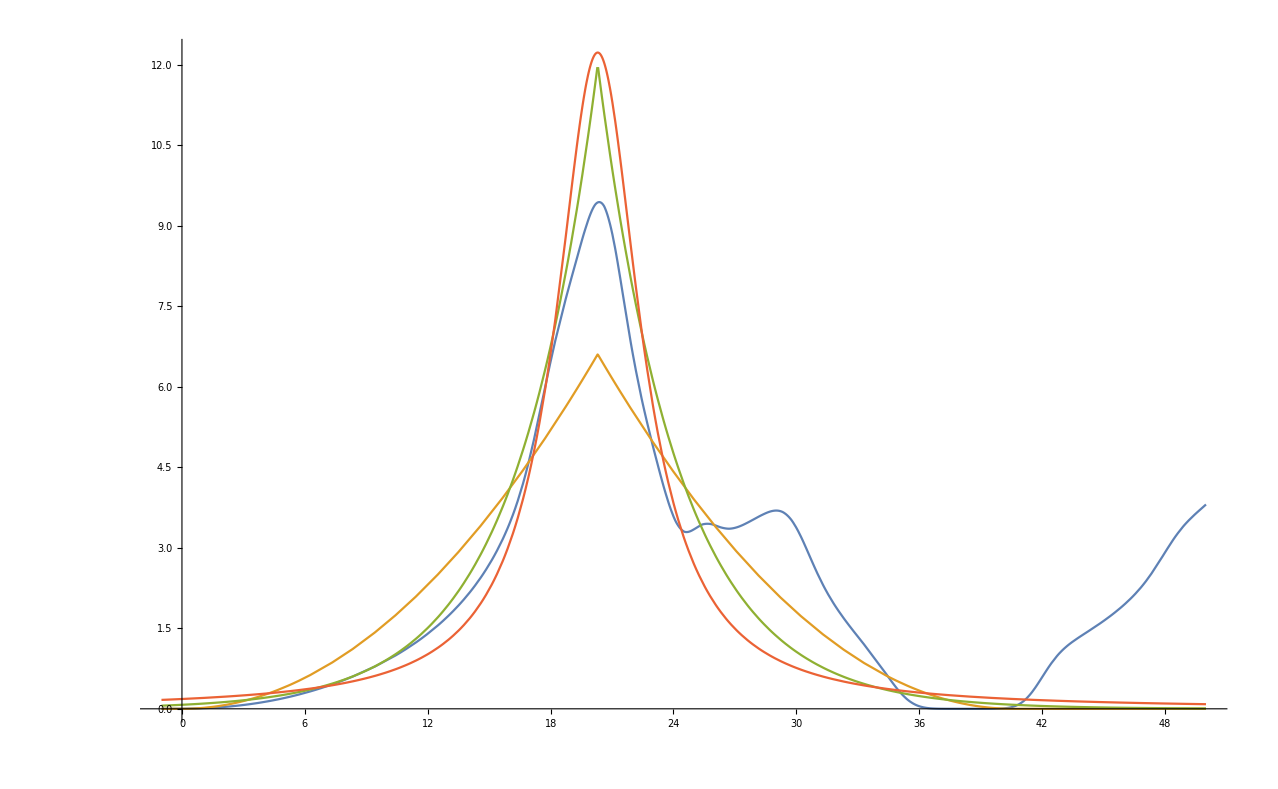

```mathematica
Plot[{THz2meV*PERFdosFITs[[9]][x*THz2meV],g[x,20.3],96PDF[LaplaceDistribution[20.3,4],x],96PDF[CauchyDistribution[20.3,2.5],x]},{x,-1,50},PlotRange->All]
```

```mathematica
Look at the
```